# Лабораторная работа 14. Аппроксимация Паде

Выполнила студентка ММФ БГУ
Вариант 8.
 1 к, 5 гр. Шклярик В.С.
 8 декабря 2021

```mathematica
c[0]=x[0]=1;
Der[1]=x[t]^2*Sin[t];
```

```mathematica
c[1]=x'[0]=Der[1]/.t->0
```

0

```mathematica
Der[2]=D[Der[1],t]
c[2]=Derivative[2][x][0]=%/.t->0
```

Cos[t] x[t]^2+2 Sin[t] x[t] x'[t]

1

```mathematica
Der[3]=D[Der[2],t]
c[3]=Derivative[3][x][0]=%/.t->0
```

-Sin[t] x[t]^2+4 Cos[t] x[t] x'[t]+2 Sin[t] x'[t]^2+2 Sin[t] x[t] x''[t]

0

```mathematica
Der[4]=D[Der[3],t]
c[4]=Derivative[4][x][0]=%/.t->0
```

-Cos[t] x[t]^2-6 Sin[t] x[t] x'[t]+6 Cos[t] x'[t]^2+6 Cos[t] x[t] x''[t]+6 Sin[t] x'[t] x''[t]+2 Sin[t] x[t] x^(3)[t]

5

```mathematica
Der[5]=D[Der[4],t]
c[5]=Derivative[5][x][0]=%/.t->0
```

Sin[t] x[t]^2-8 Cos[t] x[t] x'[t]-12 Sin[t] x'[t]^2-12 Sin[t] x[t] x''[t]+24 Cos[t] x'[t] x''[t]+6 Sin[t] x''[t]^2+8 Cos[t] x[t] x^(3)[t]+8 Sin[t] x'[t] x^(3)[t]+2 Sin[t] x[t] x^(4)[t]

0

```mathematica
ℋ=10;
Do[Print[("x")^n,"(t):= ",Der[n]=D[Der[n-1],t],"->",c[n]=Derivative[n][x][0]=Der[n]/.t->0],{n,5,ℋ}]
```

x^5(t):= Sin[t] x[t]^2-8 Cos[t] x[t] x'[t]-12 Sin[t] x'[t]^2-12 Sin[t] x[t] x''[t]+24 Cos[t] x'[t] x''[t]+6 Sin[t] x''[t]^2+8 Cos[t] x[t] x^(3)[t]+8 Sin[t] x'[t] x^(3)[t]+2 Sin[t] x[t] x^(4)[t]->0

x^6(t):= Cos[t] x[t]^2+10 Sin[t] x[t] x'[t]-20 Cos[t] x'[t]^2-20 Cos[t] x[t] x''[t]-60 Sin[t] x'[t] x''[t]+30 Cos[t] x''[t]^2-20 Sin[t] x[t] x^(3)[t]+40 Cos[t] x'[t] x^(3)[t]+20 Sin[t] x''[t] x^(3)[t]+10 Cos[t] x[t] x^(4)[t]+10 Sin[t] x'[t] x^(4)[t]+2 Sin[t] x[t] x^(5)[t]->61

x^7(t):= -Sin[t] x[t]^2+12 Cos[t] x[t] x'[t]+30 Sin[t] x'[t]^2+30 Sin[t] x[t] x''[t]-120 Cos[t] x'[t] x''[t]-90 Sin[t] x''[t]^2-40 Cos[t] x[t] x^(3)[t]-120 Sin[t] x'[t] x^(3)[t]+120 Cos[t] x''[t] x^(3)[t]+20 Sin[t] (x^(3)[t])^2-30 Sin[t] x[t] x^(4)[t]+60 Cos[t] x'[t] x^(4)[t]+30 Sin[t] x''[t] x^(4)[t]+12 Cos[t] x[t] x^(5)[t]+12 Sin[t] x'[t] x^(5)[t]+2 Sin[t] x[t] x^(6)[t]->0

x^8(t):= -Cos[t] x[t]^2-14 Sin[t] x[t] x'[t]+42 Cos[t] x'[t]^2+42 Cos[t] x[t] x''[t]+210 Sin[t] x'[t] x''[t]-210 Cos[t] x''[t]^2+70 Sin[t] x[t] x^(3)[t]-280 Cos[t] x'[t] x^(3)[t]-420 Sin[t] x''[t] x^(3)[t]+140 Cos[t] (x^(3)[t])^2-70 Cos[t] x[t] x^(4)[t]-210 Sin[t] x'[t] x^(4)[t]+210 Cos[t] x''[t] x^(4)[t]+70 Sin[t] x^(3)[t] x^(4)[t]-42 Sin[t] x[t] x^(5)[t]+84 Cos[t] x'[t] x^(5)[t]+42 Sin[t] x''[t] x^(5)[t]+14 Cos[t] x[t] x^(6)[t]+14 Sin[t] x'[t] x^(6)[t]+2 Sin[t] x[t] x^(7)[t]->1385

x^9(t):= Sin[t] x[t]^2-16 Cos[t] x[t] x'[t]-56 Sin[t] x'[t]^2-56 Sin[t] x[t] x''[t]+336 Cos[t] x'[t] x''[t]+420 Sin[t] x''[t]^2+112 Cos[t] x[t] x^(3)[t]+560 Sin[t] x'[t] x^(3)[t]-1120 Cos[t] x''[t] x^(3)[t]-560 Sin[t] (x^(3)[t])^2+140 Sin[t] x[t] x^(4)[t]-560 Cos[t] x'[t] x^(4)[t]-840 Sin[t] x''[t] x^(4)[t]+560 Cos[t] x^(3)[t] x^(4)[t]+70 Sin[t] (x^(4)[t])^2-112 Cos[t] x[t] x^(5)[t]-336 Sin[t] x'[t] x^(5)[t]+336 Cos[t] x''[t] x^(5)[t]+112 Sin[t] x^(3)[t] x^(5)[t]-56 Sin[t] x[t] x^(6)[t]+112 Cos[t] x'[t] x^(6)[t]+56 Sin[t] x''[t] x^(6)[t]+16 Cos[t] x[t] x^(7)[t]+16 Sin[t] x'[t] x^(7)[t]+2 Sin[t] x[t] x^(8)[t]->0

x^10(t):= Cos[t] x[t]^2+18 Sin[t] x[t] x'[t]-72 Cos[t] x'[t]^2-72 Cos[t] x[t] x''[t]-504 Sin[t] x'[t] x''[t]+756 Cos[t] x''[t]^2-168 Sin[t] x[t] x^(3)[t]+1008 Cos[t] x'[t] x^(3)[t]+2520 Sin[t] x''[t] x^(3)[t]-1680 Cos[t] (x^(3)[t])^2+252 Cos[t] x[t] x^(4)[t]+1260 Sin[t] x'[t] x^(4)[t]-2520 Cos[t] x''[t] x^(4)[t]-2520 Sin[t] x^(3)[t] x^(4)[t]+630 Cos[t] (x^(4)[t])^2+252 Sin[t] x[t] x^(5)[t]-1008 Cos[t] x'[t] x^(5)[t]-1512 Sin[t] x''[t] x^(5)[t]+1008 Cos[t] x^(3)[t] x^(5)[t]+252 Sin[t] x^(4)[t] x^(5)[t]-168 Cos[t] x[t] x^(6)[t]-504 Sin[t] x'[t] x^(6)[t]+504 Cos[t] x''[t] x^(6)[t]+168 Sin[t] x^(3)[t] x^(6)[t]-72 Sin[t] x[t] x^(7)[t]+144 Cos[t] x'[t] x^(7)[t]+72 Sin[t] x''[t] x^(7)[t]+18 Cos[t] x[t] x^(8)[t]+18 Sin[t] x'[t] x^(8)[t]+2 Sin[t] x[t] x^(9)[t]->50521

```mathematica
Taylor[t_]=∑_(n=0)^ℋ c[n]/(n!) t^n
```

1+t^2/2+(5 t^4)/24+(61 t^6)/720+(277 t^8)/8064+(50521 t^10)/3628800

## Построение аппроксимации Паде

```mathematica
ClearAll[Approx,num,den];
Format[a[n_Integer]]:=Subscript[a, n];
Format[b[n_Integer]]:=Subscript[b, n];
```

```mathematica
a[3]
```

0

```mathematica
ClearAll[n,t,num,den,Approx];
Approx[t_]=(num[t_]=∑_(n=0)^10 a[n] t^n)/(den[t_]=1+∑_(n=1)^10 b[n] t^n)
```

1+t^2/2+(5 t^4)/24+(61 t^6)/720+(277 t^8)/8064+(50521 t^10)/3628800

```mathematica
𝒩=20; ℳ=𝒩/2;
vars=Join[Array[a,ℳ+1,0],
Array[b,ℳ]]
```

{1,0,1/2,0,5/24,0,61/720,0,277/8064,0,50521/3628800,0,0,0,0,0,0,0,0,0,0}

```mathematica
num[t]-den[t]*Taylor[t]
```

0

```mathematica
Collect[%,t]
```

0

```mathematica
CoefficientList[%%,t]
```

{}

```mathematica
Take[%,𝒩+1]
```

Take::take: Cannot take positions 1 through 21 in {}.

Take[{},21]

```mathematica
Thread[%==0]
```

Take[{},21]==0

```mathematica
Solve[%,vars]
```

Solve::ivar: 1 is not a valid variable.

Solve[Take[{},21]==0,{1,0,1/2,0,5/24,0,61/720,0,277/8064,0,50521/3628800,0,0,0,0,0,0,0,0,0,0}]

```mathematica
Apply[Set,First@%,1]
```

Set::shape: Lists {} and 21 are not the same shape.

False

```mathematica
Approx[t]
```

1+t^2/2+(5 t^4)/24+(61 t^6)/720+(277 t^8)/8064+(50521 t^10)/3628800

## Отображение графика полинома Тейлора и аппроксимации Паде

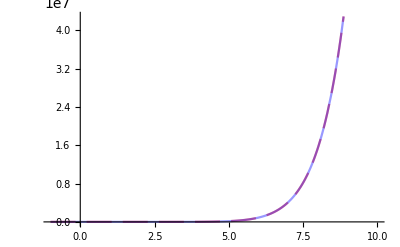

```mathematica
Plot[{Approx[t],Taylor[t]},{t,-1,10},PlotStyle->{{Pink,Dashed,AbsoluteDashing[{18,8}]},{Blue,Opacity[0.4]}}]
```